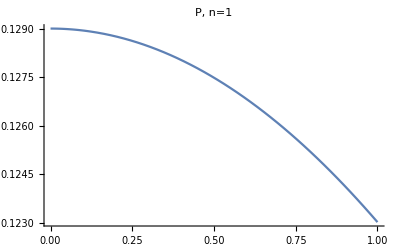

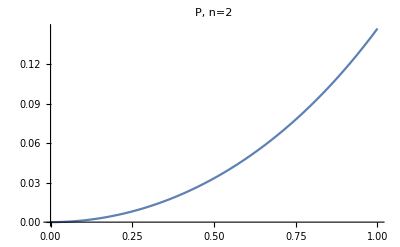

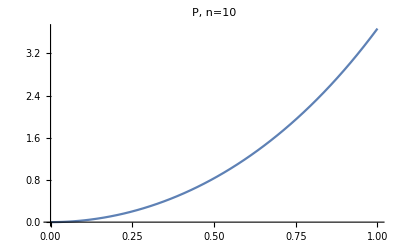

```mathematica
$Assumptions={x>0,ℏ>0,t>0,n>0,u>0,v>0};
ClearAll["Global`*"]
u=1;
ℏ=1;
Pp1=2*π*u*1^2/((v^2-ℏ^2π^2)^2)(1-(-1)^1*Cos[v]);
Pp2=2*π*u*2^2/((v^2-ℏ^2π^2)^2)(1-(-1)^2*Cos[v]);
Pp10=2*π*u*10^2/((v^2-ℏ^2π^2)^2)(1-(-1)^10*Cos[v]);
Plot[Pp1,{v,0,1},PlotLabel->"P, n=1"]
Plot[Pp2,{v,0,1},PlotLabel->"P, n=2"]
Plot[Pp10,{v,0,1},PlotLabel->"P, n=10"]
```